## Milne’s phase amplitude method

The Schrodinger equation

(-ℏ^2/(2μ)∂^2/(∂r^2)+(ℏ^2 l(l+1))/(2μ r^2)+V(r))ψ(r)=E ψ(r)

is written as:

(∂^2/(∂r^2)+(2μ)/ℏ^2(E-V(r)-(ℏ^2 l(l+1))/(2μ r^2)))ψ(r)=0

(∂^2/(∂r^2)+k^2(r))ψ(r)=0

SInce we want V(r)→-C_6/r^6, we move to scaled units where the unit of length is β_6=(2μ C_6/ℏ^2)^(1/4) and energy is measured in units of ℏ^2/2μ β_6^2.

U(r)=V(r)+(ℏ^2 l(l+1))/(2μ r^2)→-1/r^6+(l(l+1))/r^2

So

k^2(r)=ϵ+1/r^6-(l(l+1))/r^2

Milne showed [W.E. Milne, Phys. Rev. 35, 863 (1930); Am. Math. Mon. 40, 322 (1933)] that the solution can be written

ψ(r)=a α(r) sin(∫_0^r α^-2(r')ⅆr'+b)

This result is valid provided that α(r) is any particular solution to Milne’s second-order, nonlinear differential equation:

(∂^2 α(r))/(∂r^2)+k^2(r)α(r)=1/(α^3(r))

The WKB method approximates α(r)≈(k(r))^(-1/2), which would give α'=-1/2 k^(-3/2)k', and α''=-1/2 k^(-3/2)k''+3/4 k^(-5/2)(k')^2.  which, when combined with the other terms in the Milne equation suggests that α''=-1/(√(k(r)))(1/2(k''(r))/(k(r))-3/4(k'/k)^2)≈0, or (k''(r))/(k(r))≈3/2((ⅆ ln(k(r)))/ⅆr)^2.

```mathematica
U[l_,r_]:=-1/r^6+(l(l+1))/r^2
```

```mathematica
ksqr[ϵ_,l_,r_]:=ϵ-(-1/r^6+(l(l+1))/r^2)
```

```mathematica
BC1[ϵ_,l_,r_]=Simplify[ksqr[ϵ,l,r]^(-1/4)]
```

1/((1/r^6-(l (1+l))/r^2+ϵ)^(1/4))

```mathematica
BC2[ϵ_,l_,r_]=Simplify[D[ksqr[ϵ,l,r]^(-1/4),r]]
```

-(-3+l (1+l) r^4)/(2 r^7 (1/r^6-(l (1+l))/r^2+ϵ)^(5/4))

```mathematica
ϵtest=0.0;
ltest=0;
rx=0.05;
rf=3.0;αsol=NDSolve[{D[α[r],{r,2}]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,rx],α'[rx]==BC2[ϵtest,ltest,rx]},α,{r,rx,rf}]
```

{{α→InterpolatingFunction[…]}}

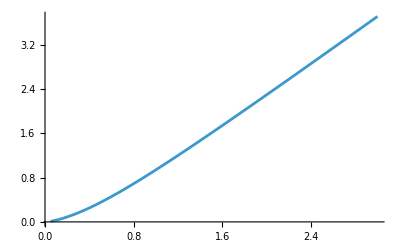

```mathematica
Plot[α[rp]/.αsol,{rp,rx,rf}]
```

```mathematica
integrand=α[rp]^-2/.αsol[[1]]
```

1/(InterpolatingFunction[…][rp])^2

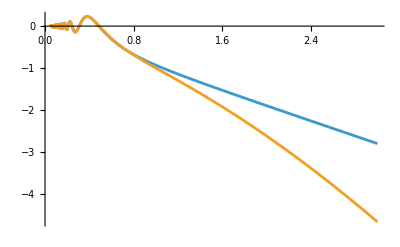

```mathematica
Plot[{α[r]Sin[NIntegrate[integrand,{rp,rx,r}]]/.αsol,1/ksqr[ϵtest,ltest,r]^(1/4)Sin[NIntegrate[ksqr[ϵtest,ltest,rp]^(1/2),{rp,rx,r}]]/.αsol},{r,rx,rf}]
```

```mathematica
p1keep=Plot[{α[r]Sin[NIntegrate[integrand,{rp,rx,r}]]/.αsol,-α[r]Cos[NIntegrate[integrand,{rp,rx,r}]]/.αsol,1/ksqr[ϵtest,ltest,r]^(1/4)Sin[NIntegrate[ksqr[ϵtest,ltest,rp]^(1/2),{rp,rx,r}]],-1/ksqr[ϵtest,ltest,r]^(1/4)Cos[NIntegrate[ksqr[ϵtest,ltest,rp]^(1/2),{rp,rx,r}]]},{r,rx,rf}]
```

$Aborted

```mathematica
χplus[L_,R_]:=√R BesselJ[-1/4(2L+1),1/(2 R^2)];
χminus[L_,R_]:=√R BesselJ[1/4(2L+1),1/(2 R^2)];
```

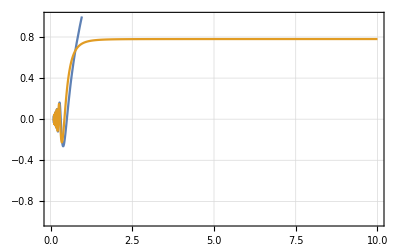

```mathematica
ltest=0;Plot[{χplus[ltest,r],χminus[ltest,r]},{r,rx,rf},Frame->True,GridLines->Automatic,LabelStyle->Large,PlotRange->{-1,1}]
```

### Finding the phase ϕ that gives the most linear independence

```mathematica
(*C6=4.274×10^3*)C6=4.300 10^3;C8=4.823×10^5;C10=6.181×10^7;
```

```mathematica
amu = (1.66053906660 10^-27)/(9.1093837015 10^-31);massK40=39.963998166amu;massRb87=86.9091805310amu;
```

```mathematica
amu
```

1822.89

```mathematica
Vlr[r_]=-C6/r^6-C8/r^8-C10/r^10;Clear[β];
```

```mathematica
Solve[Vlr[β]==-ℏ^2/(2μ β^2)/.{μ->((massK40)(massRb87))/(massK40+massRb87),ℏ->1},β]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→-144.127},{β→-5.64862-9.3801 ⅈ},{β→-5.64862+9.3801 ⅈ},{β→0.-143.737 ⅈ},{β→0.+143.737 ⅈ},{β→5.64862-9.3801 ⅈ},{β→5.64862+9.3801 ⅈ},{β→144.127}}

Scaled units for this potential amount to defining a length scale β by: V_lr(β)=ℏ^2/(2μ β^2).  This re-defines the couplings as:

c_6=(2 μ)/(ℏ^2 β^4)C_6

c_8=(2 μ)/(ℏ^2 β^6)C_8

c_10=(2 μ)/(ℏ^2 β^6)C_10

```mathematica
(*β=143.9;μ=β^4/(2C6);C8=0;C10=0*)
```

```mathematica
ℏ=1;β=144.12658703505275(*143.9*);μ=((massK40)(massRb87))/(massK40+massRb87);
c6=(2μ)/(ℏ^2 β^4)C6
c8=(2μ)/(ℏ^2 β^6)C8
c10=(2μ)/(ℏ^2 β^8)C10
```

0.994596

0.00537041

0.000033133

```mathematica
Vlr[r_]=-c6/r^6-c8/r^8-c10/r^10
```

-0.000033133/r^10-0.00537041/r^8-0.994596/r^6

```mathematica
uplots=Table[Plot[Vlr[r]+(l(l+1))/r^2,{r,0,2},PlotStyle->{Blue, Dashed},Frame->True,LabelStyle->Large,GridLines->Automatic, FrameLabel->{"r/β","U(r)/E_β"}],{l,0,20}];
```

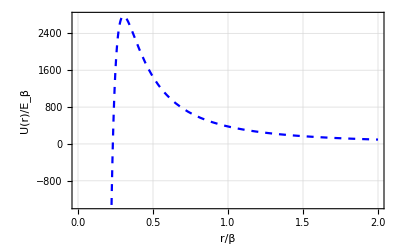

```mathematica
Show[uplots[[20]]]
```

We shall take our two reference functions to be

f^0(r)=α(r) sin(∫_r_x^r α^-2(r')ⅆr'+ϕ)

g^0(r)=-α(r) cos(∫_r_x^r α^-2(r')ⅆr'+ϕ)

This gives for the derivatives:

(ⅆf^0(r))/ⅆr=α'(r)sin(∫_r_x^r α^-2(r')ⅆr'+ϕ)+α(r) cos(∫_r_x^r α^-2(r')ⅆr'+ϕ)α^-2(r)

(ⅆf^0(r))/ⅆr=α'(r)sin(∫_r_x^r α^-2(r')ⅆr'+ϕ)+α^-1(r) cos(∫_r_x^r α^-2(r')ⅆr'+ϕ)

(ⅆf^0(r))/ⅆr=(α'(r))/(α(r))f^0(r)-1/(α^2(r)) g^0(r)

Now taking the derivative of g^0:

(ⅆg^0(r))/ⅆr=-α'(r)cos(∫_r_x^r α^-2(r')ⅆr'+ϕ)+α(r)sin(∫_r_x^r α^-2(r')ⅆr'+ϕ)α^-2(r)

(ⅆg^0(r))/ⅆr=-α'(r)cos(∫_r_x^r α^-2(r')ⅆr'+ϕ)+α^-1(r)sin(∫_r_x^r α^-2(r')ⅆr'+ϕ)

(ⅆg^0(r))/ⅆr=(α'(r))/(α(r))g^0(r)+1/(α^2(r)) f^0(r)

where, as before, α is any particular solution to:

(∂^2 α(r))/(∂r^2)+k^2(r)α(r)=1/(α^3(r))

We shall choose the solution that obeys “WKB”-like boundary conditions at r_x:

α(r_x)=1/(√(k(r_x)))

α'(r_x)=(ⅆ/ⅆr(k(r))^(-1/2))_(r=r_x)

```mathematica
ksqr[ϵ_,l_,r_]:=ϵ-(Vlr[r] +(l(l+1))/r^2)
```

```mathematica
BC1[ϵ_,l_,r_]:=Simplify[Evaluate[(ϵ-(Vlr[r] +(l(l+1))/r^2))^(-1/4)]]
```

```mathematica
BC2[ϵ_,l_,r_]:=Simplify[Evaluate[D[(ϵ-(Vlr[r] +(l(l+1))/r^2))^(-1/4),r]]]
```

```mathematica
rx=0.05;ltest=0;{α''[r]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,r]/.r->rx,α'[rx]==BC2[ϵtest,ltest,r]/.r->rx}
```

{-1/α[r]^3+(0.+0.000033133/r^10+0.00537041/r^8+0.994596/r^6) α[r]+α''[r]==0,α[0.1]==0.0270675,α'[0.1]==0.493167}

```mathematica
ϵtest=0.0;(*6.547 10^-3;*)
ltest=0;
rx=0.05;
rf=3.0;αsol=NDSolve[{α''[r]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,r]/.r->rx,α'[rx]==BC2[ϵtest,ltest,r]/.r->rx},α,{r,rx,rf},AccuracyGoal->{15}][[1]];
```

```mathematica
nr=100;(*logrGrid=Table[Log[rx]+(i-1)/(nr-1)(Log[rf]-Log[rx]),{i,1,nr}];
rGrid=Exp[logrGrid];*)
rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];αtable=Table[{rGrid[[i]],α[r]/.αsol/.r->rGrid[[i]]},{i,1,nr}];
αptable=Table[{rGrid[[i]],D[α[r]/.αsol,r]/.r->rGrid[[i]]},{i,1,nr}];
PhaseIntTable=Flatten[{0,Table[NIntegrate[α[rp]^-2/.αsol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}];
```

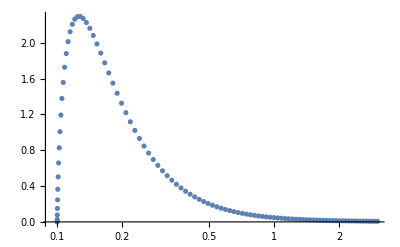

```mathematica
ListLogLinearPlot[Transpose[{rGrid,PhaseIntTable}],PlotRange->All]
```

```mathematica
f0table=Table[{rGrid[[i]],αtable[[i,2]]Sin[Total[PhaseIntTable[[1;;i]]]]},{i,1,nr}];
g0table=Table[{rGrid[[i]],-αtable[[i,2]]Cos[Total[PhaseIntTable[[1;;i]]]]},{i,1,nr}];
```

```mathematica
g0table[[1]]
```

{0.1,-0.0270675}

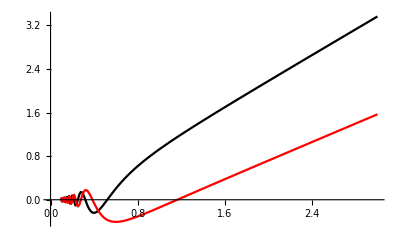

```mathematica
plistfg=ListPlot[{f0table,g0table},PlotStyle->{Black,Red},Joined->True]
```

Now using (ⅆf^0(r))/ⅆr=(α'(r))/(α(r))f^0(r)-1/(α^2(r)) g^0(r)
(ⅆg^0(r))/ⅆr=(α'(r))/(α(r))g^0(r)+1/(α^2(r)) f^0(r)

```mathematica
f0ptable=Table[{rGrid[[i]],αptable[[i,2]]/αtable[[i,2]] f0table[[i,2]]-1/αtable[[i,2]]^2 g0table[[i,2]]},{i,1,nr}];
g0ptable=Table[{rGrid[[i]],αptable[[i,2]]/αtable[[i,2]] g0table[[i,2]]+1/αtable[[i,2]]^2 f0table[[i,2]]},{i,1,nr}];
```

```mathematica
(*f0ptable=Table[{rGrid[[i]],(f0table[[i+1,2]]-f0table[[i,2]])/(rGrid[[i+1]]-rGrid[[i]])},{i,1,numr-1}];
g0ptable=Table[{rGrid[[i]],(g0table[[i+1,2]]-g0table[[i,2]])/(rGrid[[i+1]]-rGrid[[i]])},{i,1,numr-1}];*)
```

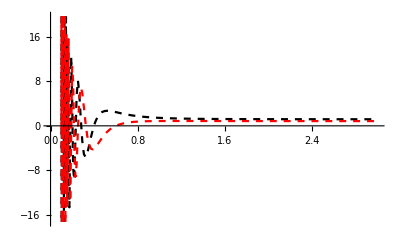

```mathematica
plistfpgp=ListPlot[{f0ptable,g0ptable},Joined->True,PlotStyle->{{Black,Dashed},{Red,Dashed}}]
```

Now to determine what value of ϕ gives the best base pair with the most linear independence. The expression we need is:

tan ϕ = (- W(χ_-(r),g_(ϕ=0)^0(r)))/(W(χ_-(r),f_(ϕ=0)^0(r)))

```mathematica
χmprime[L_,r_]=D[χminus[L,r],r];χminustable=Table[{rGrid[[i]],χminus[ltest,rGrid[[i]]]},{i,1,nr}];χminusprimetable=Table[{rGrid[[i]],χmprime[ltest,rGrid[[i]]]},{i,1,nr}];
χpprime[L_,r_]=D[χplus[L,r],r];χplustable=Table[{rGrid[[i]],χplus[ltest,rGrid[[i]]]},{i,1,nr}];χplusprimetable=Table[{rGrid[[i]],χmprime[ltest,rGrid[[i]]]},{i,1,nr}];
```

```mathematica
tanphitableminus=Table[{rGrid[[i]],-(χminustable[[i,2]]g0ptable[[i,2]]-χminusprimetable[[i,2]]g0table[[i,2]])/(χminustable[[i,2]]f0ptable[[i,2]]-χminusprimetable[[i,2]]f0table[[i,2]])},{i,1,nr-1}];
```

```mathematica
tanphitableplus=Table[{rGrid[[i]],(χplustable[[i,2]]f0ptable[[i,2]]-χplusprimetable[[i,2]]f0table[[i,2]])/(χplustable[[i,2]]g0ptable[[i,2]]-χplusprimetable[[i,2]]g0table[[i,2]])},{i,1,nr-1}];
```

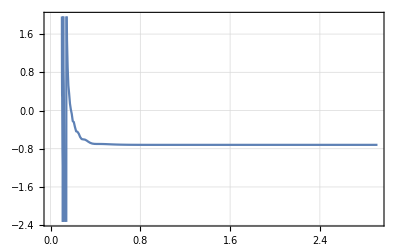

```mathematica
ListPlot[tanphitableminus,Frame->True,GridLines->Automatic,LabelStyle->Large,PlotRange->{Automatic,Automatic},Joined->True]
```

```mathematica
tanphitableminus[[nr-1,2]]
```

-0.718599

```mathematica
TrigReduce[Simplify[Normal[Series[√R BesselJ[1/4(2l+1),1/x],{x,0,2}]],{x>0}]/.x->2 R^2]
```

1/(8 √π)(-3 R^2 √(R^3) Cos[π/8-(l π)/4+1/(2 R^2)]+4 l R^2 √(R^3) Cos[π/8-(l π)/4+1/(2 R^2)]+4 l^2 R^2 √(R^3) Cos[π/8-(l π)/4+1/(2 R^2)]+16 √(R^3) Sin[π/8-(l π)/4+1/(2 R^2)])

For a potential with ONLY the C_6/r^6 we get:

```mathematica
Tan[-1/(2 rx^2)+ltest π/4-5 π/8]
```

7.81816

```mathematica
ϕ=ArcTan[tanphitableminus[[nr-1,2]]]
```

-0.6231

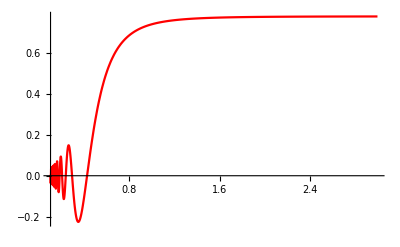

```mathematica
pchim=Plot[χminus[ltest,r],{r,rx,rf},PlotStyle->Red,PlotRange->All]
```

```mathematica
Cos[ϕ]
```

0.812073

```mathematica
ϕ
```

-0.6231

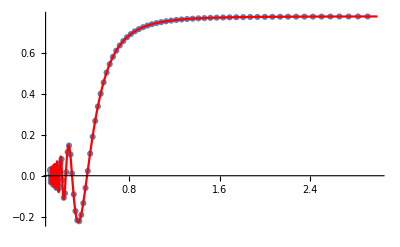

```mathematica
norm=χminus[ltest,rGrid[[nr]]]/(Cos[ϕ]g0table[[nr,2]]+Sin[ϕ]f0table[[nr,2]]);Show[ListPlot[Table[{rGrid[[i]],norm(Cos[ϕ]g0table[[i,2]]+Sin[ϕ]f0table[[i,2]])},{i,1,nr-1}],PlotRange->All],pchim,PlotRange->Automatic(*{-10^-3,10^-3}*)]
```

```mathematica
f0tablefinal=Table[{rGrid[[i]],norm αtable[[i,2]]Sin[ϕ+Total[PhaseIntTable[[1;;i]]]]},{i,1,nr}];
g0tablefinal=Table[{rGrid[[i]],-norm αtable[[i,2]]Cos[ϕ+Total[PhaseIntTable[[1;;i]]]]},{i,1,nr}];
```

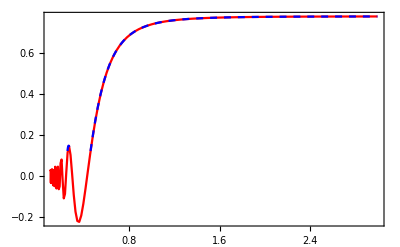

```mathematica
pfg=ListPlot[g0tablefinal,Joined->True,PlotStyle->{Red}];
pU=Plot[{χminus[ltest,r]},{r,rx,rf},PlotStyle->{Blue,Dashed}];
Show[pfg,pU,PlotRange->Automatic,Frame->True]
```

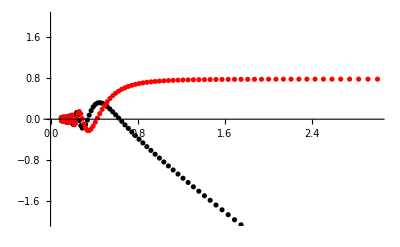

```mathematica
ListPlot[{f0tablefinal,g0tablefinal},PlotStyle->{Black,Red},PlotRange->{-2,2}]
```

```mathematica
ϵtest=(*0.0;*)6.547 10^-3;
ltest=0;
rx=0.05;
rf=3.0;αsol=NDSolve[{α''[r]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,r]/.r->rx,α'[rx]==BC2[ϵtest,ltest,r]/.r->rx},α,{r,rx,rf}][[1]];
nr=200;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];αtable=Table[{rGrid[[i]],α[r]/.αsol/.r->rGrid[[i]]},{i,1,nr}];
PhaseIntTable=Flatten[{0,Table[NIntegrate[α[rp]^-2/.αsol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}];
ListPlot[PhaseIntTable,PlotRange->All];
f0table=Table[{rGrid[[i]],αtable[[i,2]]Sin[ϕ+Total[PhaseIntTable[[1;;i]]]]},{i,1,nr}];
g0table=Table[{rGrid[[i]],-αtable[[i,2]]Cos[ϕ+Total[PhaseIntTable[[1;;i]]]]},{i,1,nr}];
```

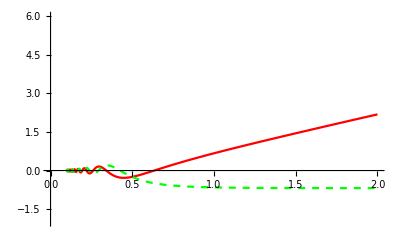

```mathematica
indepfplot=ListPlot[{f0table,g0table},Joined->True,PlotRange->{-2,6},PlotStyle->{{Red},{Green,Dashed}}]
```

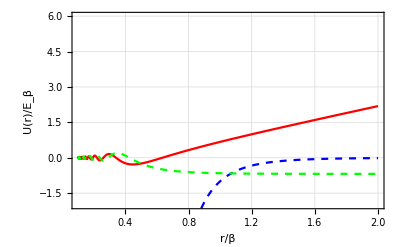

```mathematica
Show[uplots[[ltest+1]],indepfplot,Frame->True,PlotRange->{{rx,rf},{-2,6}}]
```

### Let’s try to find the phases for all partial waves together

```mathematica
χplus[L_,R_]:=√R BesselJ[-1/4(2L+1),1/(2 R^2)];
χminus[L_,R_]:=√R BesselJ[1/4(2L+1),1/(2 R^2)];
```

```mathematica
ksqr[ϵ_,l_,r_]:=ϵ-(Vlr[r] +(l(l+1))/r^2)
```

```mathematica
BC1[ϵ_,l_,r_]=Simplify[Evaluate[(ksqr[ϵ,l,r])^(-1/4)]]
```

1/((0.000033133/r^10+0.00537041/r^8+0.994596/r^6-(l (1+l))/r^2+ϵ)^(1/4))

```mathematica
BC2[ϵ_,l_,r_]=Simplify[Evaluate[D[(ksqr[ϵ,l,r])^(-1/4),r]]]
```

-(0.5 (-0.000165665-0.0214816 r^2-2.98379 r^4+l (1+l) r^8))/(r^11 (0.000033133/r^10+0.00537041/r^8+0.994596/r^6-(l (1+l))/r^2+ϵ)^(5/4))

```mathematica
ϵtest=0.0;
rx=0.05;
rf=3.0;
```

```mathematica
αsol=Flatten[Table[NDSolve[{α''[r]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,rx],α'[rx]==BC2[ϵtest,ltest,rx]},α,{r,rx,rf}],{ltest,0,20}]];
```

```mathematica
αfun=Table[α/.αsol[[i]],{i,1,Length[αsol]}];
```

```mathematica
nr=100;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
```

```mathematica
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(αfun[[ltest+1]][rp])^-2/.αsol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,20}];
```

```mathematica
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,20}];
```

Now using (ⅆf^0(r))/ⅆr=(α'(r))/(α(r))f^0(r)-1/(α^2(r)) g^0(r)
(ⅆg^0(r))/ⅆr=(α'(r))/(α(r))g^0(r)+1/(α^2(r)) f^0(r)

```mathematica
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=D[α[rp],rp]/.rp->r;
g0=-α[r]Cos[ϕ+phaseint[r]];
f0=α[r]Sin[ϕ+phaseint[r]];
f0p=αp/α[r] f0-1/α[r]^2 g0;
g0p=αp/α[r] g0+1/α[r]^2 f0;
χm=χminus[l,r];
χmp=χmprime[l,r];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
tanphi=Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,αfun[[ltest+1]],phaseintfun[[ltest+1]],1rf];-(χm g0p-χmp g0)/(χm f0p-χmp f0),{ltest,0,20}]
```

{-0.718596,0.152041,1.3024,-9.76914,-0.876752,0.0216497,0.9426,11.3633,-1.36422,-0.228423,0.523932,2.45088,-3.15292,-0.648409,0.107564,0.996474,8.5422,-1.63711,-0.380072,0.298917,1.36526}

{-0.718596, 0.152041, 1.3024, -9.76914, -0.876752, 0.0216498, 0.9426, 11.3633, -1.36422, -0.228423, 0.523932, 2.45088, -3.15292, -0.648409, 0.107564, 0.996474, 8.54221, -1.63711, -0.380072, 0.298917, 1.36526}

```mathematica
ϕvals=ArcTan[tanphi]
```

{-0.623098,0.150886,0.915993,-1.46879,-0.719822,0.0216464,0.755859,1.48302,-0.93825,-0.22457,0.482609,1.1834,-1.26367,-0.575256,0.107152,0.783632,1.45426,-1.02245,-0.36321,0.290463,0.938614}

```mathematica
g0function[ϕ_,α_,phaseintfun_,r_]:=-α[r]Cos[ϕ+phaseintfun[r]]
```

```mathematica
f0function[ϕ_,α_,phaseintfun_,r_]:=α[r]Sin[ϕ+phaseintfun[r]]
```

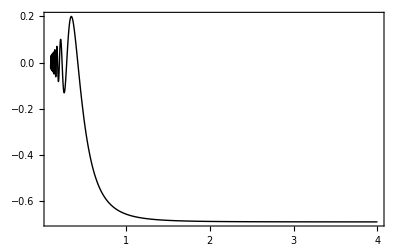

```mathematica
ltest=0;Plot[g0function[ϕvals[[ltest+1]],αfun[[ltest+1]],phaseintfun[[ltest+1]],r],{r,rx,rf},PlotRange->All,PlotStyle->{Black,Thin},Frame->True]
```

### Addition of short-range square well potential

```mathematica
r0=0.2;kin=√(V0+ϵ)/.{ϵ->0.0,V0->10/r0^6};logdersquare[l_,V0_,r0_,ϵ_]:=Module[{kin,r},
kin=√(V0+ϵ);
D[ Log[r SphericalBesselJ[l,kin r]],r]/.r->r0
]
```

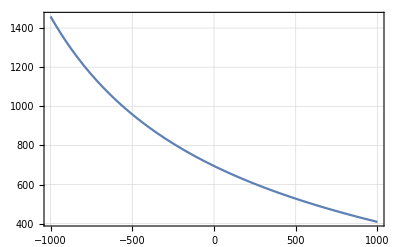

```mathematica
Plot[logdersquare[0,10/r0^6,r0,ϵ],{ϵ,-1000,1000},Frame->True,GridLines->Automatic]
```

```mathematica
rx=0.05;
rf=3.0;
nr=100;
rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];(*logrGrid=Table[Log[rx]+(i-1)/(nr-1)(Log[rf]-Log[rx]),{i,1,nr}];
rGrid=Exp[logrGrid];*)
```

```mathematica
Clear[α]
```

```mathematica
ϵtest=0.01;αsol=Flatten[Table[NDSolve[{α''[r]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,rx],α'[rx]==BC2[ϵtest,ltest,rx]},α,{r,rx,rf}],{ltest,0,20}]];
```

```mathematica
αfun=Table[α/.αsol[[i]],{i,1,Length[αsol]}];
```

```mathematica
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(αfun[[ltest+1]][rp])^-2/.αsol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,20}];
```

```mathematica
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,20}];
```

```mathematica
Clear[α]
```

```mathematica
QuantumDefectSquare[ϕ_,l_,r0_,V0_,ϵ_]:=Module[{α,rp,αrule,αfun,rx,rf,phaseint,f0,g0,f0p,g0p,αp,χm,χmp,logder,Ksr},
rx=0.05;
rf=r0;
αrule=NDSolve[{α''[r]+ksqr[ϵ,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵ,l,rx],α'[rx]==BC2[ϵ,l,rx]},α,{r,rx,rf}];
αfun=α/.αrule[[1]];

phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,r0}];
αp=D[αfun[rp],rp]/.rp->r0;
g0=-α[r0]Cos[ϕ+phaseint];
f0=α[r0]Sin[ϕ+phaseint];
f0p=αp/αfun[r0] f0-1/αfun[r0]^2 g0;
g0p=αp/αfun[r0] g0+1/αfun[r0]^2 f0;
χm=χminus[l,r0];
χmp=χmprime[l,r0];
logder=logdersquare[l,V0,r0,ϵ];
Ksr=(logder f0-f0p)/(logder g0-g0p);
{Ksr,ArcTan[Ksr]/π}
]
```

```mathematica
ϵvals={-1000.0,-750.0,-500.0,-250.0,0.0,250.0,500.0,750.0,1000.0};μTable=Table[Table[{ϵ,QuantumDefectSquare[ϕvals[[l+1]],ltest,r0,10/r0^6,ϵ][[2]]},{ϵ,ϵvals}],{l,0,20}];
```

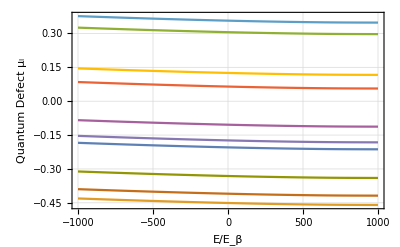

```mathematica
ListPlot[μTable[[1;;10]],Joined->True,InterpolationOrder->3,Frame->True,GridLines->Automatic,LabelStyle->Large,FrameLabel->{"E/E_β","Quantum Defect μ_l"}]
```

```mathematica
KsrTable=Table[Table[{ϵ,QuantumDefectSquare[ϕvals[[l+1]],ltest,r0,10/r0^6,ϵ][[1]]},{ϵ,ϵvals}],{l,0,20}];
```

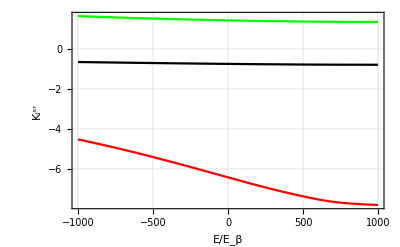

```mathematica
ListPlot[KsrTable[[1;;3]],PlotStyle->{Black,Red,Green},Joined->True,InterpolationOrder->3,Frame->True,GridLines->Automatic,LabelStyle->Large,FrameLabel->{"E/E_β","K_l^sr"}]
```

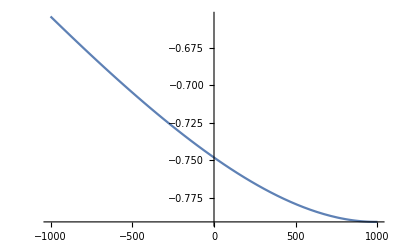

```mathematica
Ksrfun=Table[Interpolation[KsrTable[[l+1]]],{l,0,20}];
Plot[Ksrfun[[1]][r],{r,ϵvals[[1]],ϵvals[[Length[ϵvals]]]}]
```

```mathematica
QuantumDefectParameters[ϕ_,l_,rfinal_,ϵ_]:=Module[{rjl,rjlp,ryl,rylp,𝒜,𝒢,tanη,g,gp,k,α,rp,αrule,αfun,rx,phaseint,f0,g0,f0p,g0p,αp,χm,χmp,γ,Ksr,Wrjf0,Wryf0,Wgg0,Wgf0},
rx=0.05;
k=√ϵ;
rjl=k rfinal SphericalBesselJ[l,k rfinal];
rjlp=D[k rp SphericalBesselJ[l,k rp],rp]/.rp->rfinal;
ryl= k rfinal SphericalBesselY[l,k rfinal];
rylp=D[k rp SphericalBesselY[l,k rp],rp]/.rp->rfinal;
g=√(k/π) rfinal SphericalBesselY[l,k rfinal];
gp=D[√(k/π)  rp SphericalBesselY[l,k rp],rp]/.rp->rfinal;
αrule=NDSolve[{α''[r]+ksqr[ϵ,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵ,l,rx],α'[rx]==BC2[ϵ,l,rx]},α,{r,rx,rfinal}];
αfun=α/.αrule[[1]];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rfinal}];
αp=D[αfun[rp],rp]/.rp->rfinal;
g0=-αfun[rfinal]Cos[ϕ+phaseint];
f0=αfun[rfinal]Sin[ϕ+phaseint];
f0p=αp/αfun[rfinal] f0-1/αfun[rfinal]^2 g0;
g0p=αp/αfun[rfinal] g0+1/αfun[rfinal]^2 f0;
Wrjf0=rjl f0p - rjlp f0;
Wryf0=ryl f0p - rylp f0;
Wgg0=g g0p - gp g0;
Wgf0=g f0p - gp f0;
tanη=Wrjf0/Wryf0;
𝒜=k/(Wrjf0^2+Wryf0^2);
𝒢=-Wgg0/Wgf0;
{tanη,𝒜,𝒢}
]
```

```mathematica
QuantumDefectParametersBound[ϕ_,l_,rfinal_,ϵ_]:=Module[{tanγ,gbound,gboundp,k,κ,α,rp,αrule,αfun,rx,phaseint,f0,g0,f0p,g0p,αp,γ},
rx=0.05;
k=√ϵ;
κ=√-ϵ;
gbound=√(2/π κ rp)BesselK[l+1/2,κ rp]/.rp->rfinal;
gboundp=D[√(2/π κ rp)BesselK[l+1/2,κ rp],rp]/.rp->rfinal;
(*gbound=Exp[-κ rfinal];
gboundp=-κ gbound;*)
αrule=NDSolve[{α''[r]+ksqr[ϵ,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵ,l,rx],α'[rx]==BC2[ϵ,l,rx]},α,{r,rx,rfinal}];
αfun=α/.αrule[[1]];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rfinal}];
αp=D[αfun[rp],rp]/.rp->rfinal;
g0=-αfun[rfinal]Cos[ϕ+phaseint];
f0=αfun[rfinal]Sin[ϕ+phaseint];
f0p=αp/αfun[rfinal] f0-1/αfun[rfinal]^2 g0;
g0p=αp/αfun[rfinal] g0+1/αfun[rfinal]^2 f0;
tanγ=-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
{tanγ}
]
```

```mathematica
γ0table=Table[{ϵ,ArcTan[QuantumDefectParametersBound[ϕvals[[ltest+1]],ltest,rf,ϵ][[1]]]},{ϵ,-1000.0001,0.0001,10}];
```

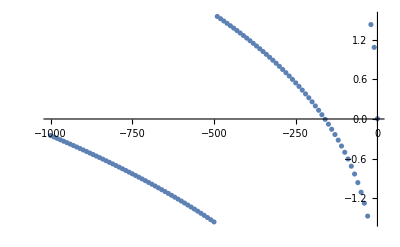

```mathematica
ListPlot[γ0table]
```

```mathematica
γ0tablenew=γ0table;
For[i=Length[γ0table],i>1,i--,
If[(γ0table[[i-1,2]]-γ0table[[i,2]]<-1.2),Print[i];
γ0tablenew[[1;;i-1,2]]=γ0tablenew[[1;;i-1,2]]+π,γ0tablenew[[1;;i-1,2]]=γ0tablenew[[1;;i-1,2]]]
]
```

99

52

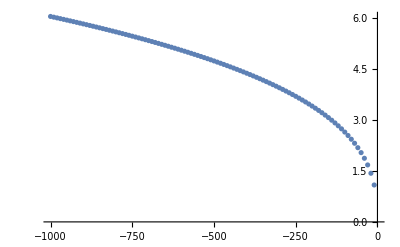

```mathematica
ListPlot[γ0tablenew]
```

```mathematica
γfun=Interpolation[γ0tablenew]
```

InterpolatingFunction[{{-1000., -0.0001}}, <>]

```mathematica
ltest
```

0

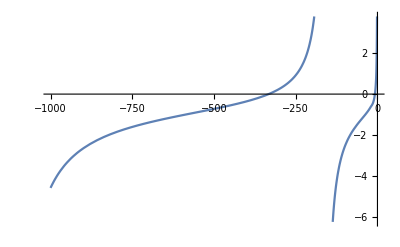

```mathematica
Plot[Ksrfun[[ltest+1]][ϵ]+Cot[γfun[ϵ]],{ϵ,-1000.0,0}]
```

```mathematica
LowBindingtanγtable=Table[{-ϵ,ArcTan[QuantumDefectParametersBound[ArcTan[tanphi[[ltest+1]]],ltest,rf,ϵ][[1]]]},{ϵ,-1,0.00001,.03}];
```

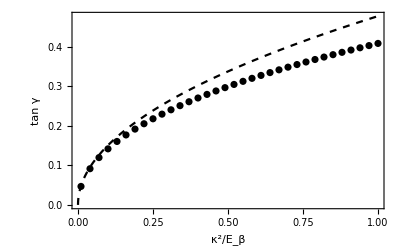

```mathematica
Show[Plot[If[ltest==0,abar[ltest] √ϵ,ϵ/((2ltest+3)(2ltest-1))],{ϵ,0,1},PlotStyle->{Black,Dashed}],ListPlot[LowBindingtanγtable,PlotStyle->Black],Frame->True,FrameLabel->{"κ^2/E_β","tan γ"}]
```

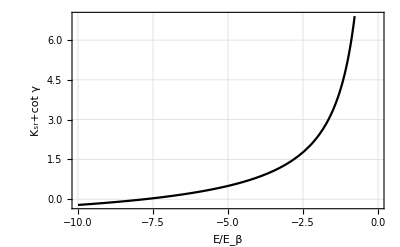

```mathematica
Plot[(Ksrfun[[ltest+1]][ϵ]+Cot[γfun[ϵ]]),{ϵ,-10.0,0},Frame->True,LabelStyle->Large,FrameLabel->{"E/E_β","K_sr+cot γ"},GridLines->Automatic,PlotStyle->Black]
```

```mathematica
pos=FindRoot[Ksrfun[[ltest+1]][ϵ]+Cot[γfun[ϵ]],{ϵ,-4.0}]
```

{ϵ→-7.76556}

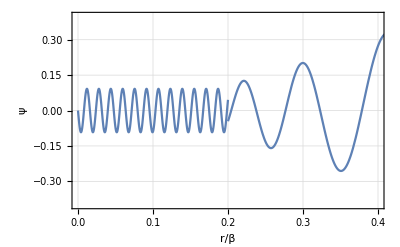

```mathematica
Clear[α];ϵtest=ϵ/.pos;αrule=NDSolve[{α''[r]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,rx],α'[rx]==BC2[ϵtest,ltest,rx]},α,{r,rx,rf}];
αfun=α/.αrule[[1]];
PhaseInt=Flatten[{0,Table[NIntegrate[αfun[rp]^-2/.αrule,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}];
phaseintfun=Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]];
Show[Plot[(r SphericalBesselJ[ltest,√(ϵtest+10/r0^6)r])1/(r0 SphericalBesselJ[ltest,√(ϵtest+10/r0^6)r0])(f0function[ϕvals[[ltest+1]],αfun,phaseintfun,r0]-Ksrfun[[ltest+1]][ϵtest]g0function[ϕvals[[ltest+1]],αfun,phaseintfun,r0]),{r,0,r0}], Plot[
(f0function[ϕvals[[ltest+1]],αfun,phaseintfun,r]-Ksrfun[[ltest+1]][ϵtest]g0function[ϕvals[[ltest+1]],αfun,phaseintfun,r]),{r,r0,rf}],PlotRange->{{0,.4},{-.4,.4}},Frame->True,GridLines->Automatic,LabelStyle->Large,FrameLabel->{"r/β","ψ"}]
```

Let’s consider just the bound state problem.  There are three regions.  At short range, we assume there is some known ψ_sr(r).  For the square-well problem

ψ_sr(r)=B r j_l(k_in r)

At “long range”

ψ_lr(r)=C (f^0-tan(πμ)g^0)

Demanding that these be equal at some value r_0, we have

r j_l(k_in r)=C/B (f^0-tan(πμ)g^0)

So,

W(r j_l(k_in r), f^0)=-C/Btan(πμ)W(g^0,f^0)

-C/Btan(πμ)=(W(r j_l(k_in r), f^0))/(W(g^0,f^0))

(W(r j_l(k_in r), g^0))/(W(f^0,g^0))=C/B

so that:

(W(r j_l(k_in r), f^0))/(W(g^0,f^0))=-(W(r j_l(k_in r), g^0))/(W(f^0,g^0))tan(πμ)

tan(πμ)=((W(r j_l(k_in r), f^0))/(W(r j_l(k_in r), g^0)))_(r=r_0)

Now finally, at some sufficiently large r,

ψ_vlr(r)=D ⅇ^(-κ r)

Matching ψ_lr to this form at some large r_f gives:

C/B (f^0-tan(πμ)g^0)=D ⅇ^(-κ r)

Since D is unknown anyhow, so is the product D B/C, therefore, just absorb B/C into D.

(f^0-tan(πμ)g^0)=D ⅇ^(-κ r)

(W(f^0,g^0))/(W(ⅇ^(-κ r),g^0))=D

The Wronskian with f^0 gives:

(W(f^0,g^0))/(W(ⅇ^(-κ r),g^0)) (W(ⅇ^(-κ r),f^0))/(W(g^0,f^0))=-tan(πμ)

So that

(W(ⅇ^(-κ r),f^0))/(W(ⅇ^(-κ r),g^0)) =tan(πμ)

(W(ⅇ^(-κ r),f^0))/(W(ⅇ^(-κ r),g^0)) -tan(πμ)=0

(W(ⅇ^(-κ r),f^0))/(W(ⅇ^(-κ r),g^0))=-cotγ, while tanπμ=K^sr

cot γ +K^sr=0

Seems like the bound state condition reduces to the roots of:

```mathematica
nr=100;
rx=0.05;
r0=0.2;
rf=3.0;
rGrid=
rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
```

```mathematica
abar[L_]:=((π 2^(-(2L+3/2)))/(Gamma[L/2+5/4]Gamma[L+1/2]))^(2/(2L+1))
```

```mathematica
ltest=0;ktable=Table[k,{k,0.001,1,.1}];lowEparameters=Table[QuantumDefectParameters[ArcTan[tanphi[[ltest+1]]],ltest,rf,k^2][[1;;3]],{k,ktable}]
```

{{-0.000487615,0.000474038,0.00038982},{-0.049332,0.0477928,0.00371614},{-0.0986632,0.0946195,0.0135032},{-0.14896,0.140506,0.0295815},{-0.200695,0.185076,0.0517011},{-0.254341,0.228043,0.0795775},{-0.310374,0.26922,0.112939},{-0.36929,0.308515,0.151576},{-0.431622,0.345911,0.195387},{-0.497966,0.38145,0.244407}}

```mathematica
ηplot1=ListPlot[Table[{ktable[[i]],ArcTan[lowEparameters[[i,1]]]},{i,1,Length[ktable]}],PlotStyle->Black];
```

Compare this to the small k form:

```mathematica
ηplot2=Plot[(-1)^(L+1)(abar[L] k)^(2L+1)+ (3π Gamma[L-3/2])/(32 Gamma[L+7/2])k^4/.L->ltest,{k,0,1},PlotStyle->{Black,Dashed}];
```

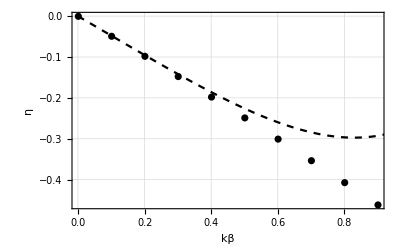

```mathematica
Show[ηplot1,ηplot2,Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"kβ","η"}]
```

```mathematica
Ahalfplot1=ListPlot[Table[{ktable[[i]],-√lowEparameters[[i,2]]},{i,1,Length[ktable]}],PlotStyle->Black];
Ahalfplot2=Plot[-(abar[L] k)^(L+1/2)/.L->ltest,{k,0,1},PlotStyle->{Black,Dashed}];
```

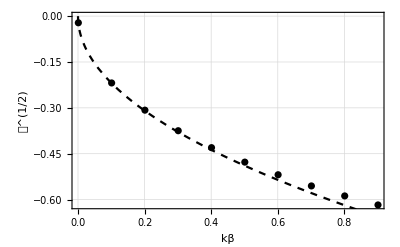

```mathematica
Show[Ahalfplot1,Ahalfplot2,Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"kβ","𝒜^(1/2)"}]
```

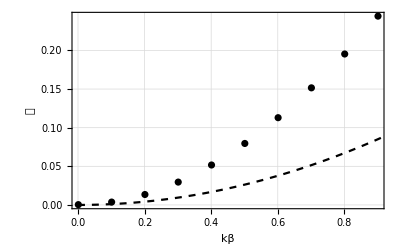

```mathematica
Gplot1=ListPlot[Table[{ktable[[i]],lowEparameters[[i,3]]},{i,1,Length[ktable]}],PlotStyle->Black];
Gplot2=Plot[-k^2/((2L+3)(2L-1))+(-1)^(L+1)(abar[ltest] k)^(4L+2)/.L->ltest,{k,0,1},PlotStyle->{Black,Dashed}];
Show[Gplot1,Gplot2,Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"kβ","𝒢"}]
```

This calculation agrees with the small k form for G given in the Ruzic paper and thesis, but only for L>0.  For the L=0 case, both terms in the small k expression go as k^2 and the numerical calculation does NOT agree.  Let’s work through the derivation to see if we can verify the expression.

### Derivation of small k form for 𝒢.

From the PRA [PRA 87 032706 (2013)] Eq. B11:

f

I’ll assume that their expressions for the asymptotic forms of f̂,ĝ are correct (Eq. B19)

f̂→^(r>>1, E→0)-√a(r/a)^(l+1)/((2l+1)!!)+(-1)^l √a((2l-1)!!)/(r/a)^l

ĝ→^(r>>1, E→0)√a((2l-1)!!)/(r/a)^l(1+(E r^2)/(4l-2)+((-1)^l E)/((2l+3)(2l-1)))-E/((2l+3)(2l-1))√a(r/a)^(l+1)/((2l+1)!!)

#### Bound state case

Starting with Eq. B24

tan γ f̂+ĝ→^(r >> 1)D ⅇ^(-κ r)

Plugging in the asymptotic forms:

tan γ (-√a(r/a)^(l+1)/((2l+1)!!)+(-1)^l √a((2l-1)!!)/(r/a)^l)+(√a((2l-1)!!)/(r/a)^l(1+(-κ^2 r^2)/(4l-2)-((-1)^l κ^2)/((2l+3)(2l-1)))+κ^2/((2l+3)(2l-1))√a(r/a)^(l+1)/((2l+1)!!))=D ∑_n (-κ r)^n/(n!)

tan γ ((-√a)/((2l+1)!!)(r/a)^(l+1)+(-1)^l √a(2l-1)!!(r/a)^-l)+(√a(2l-1)!!(r/a)^-l+(-√a(2l-1)!!κ^2 r^2)/(4l-2)(r/a)^-l-(√a(2l-1)!!(-1)^l κ^2)/((2l+3)(2l-1))(r/a)^-l+(κ^2 √a)/((2l+3)(2l-1)(2l+1)!!)(r/a)^(l+1))=D ∑_n (-κ r)^n/(n!)

tan γ (-1/((2l+1)!!)^2(r/a)^(l+1)+(-1)^l(r/a)^-l)+((r/a)^-l+(-κ^2 a^2)/(4l-2)(r/a)^(-l+2)-((-1)^l κ^2)/((2l+3)(2l-1))(r/a)^-l+κ^2/((2l+3)(2l-1)((2l+1)!!)^2)(r/a)^(l+1))=D/((2l-1)!!√a)  (1-κ r+(κ r)^2/2+...+(-κ r)^n/(n!))

Now multiply through by (r/a)^l

tan γ (-1/((2l+1)!!)^2(r/a)^(2l+1)+(-1)^l)+(1+(-κ^2 a^2)/(4l-2)(r/a)^2-((-1)^l κ^2)/((2l+3)(2l-1))+κ^2/((2l+3)(2l-1)((2l+1)!!)^2)(r/a)^(2l+1))=D/((2l-1)!!√a)(r/a)^l  (1-κ r+(κ r)^2/2+...+(-κ r)^n/(n!))

tan γ (-1/((2l+1)!!)^2(r/a)^(2l+1)+(-1)^l)+(1+(-κ^2 r^2)/(4l-2)-((-1)^l κ^2)/((2l+3)(2l-1))+κ^2/((2l+3)(2l-1)((2l+1)!!)^2)(r/a)^(2l+1))=D/((2l-1)!!a^(l+1/2)) (r^l-κ r^(l+1)+(κ^2 r^(l+2))/2+...+((-κ)^n r^(l+n))/(n!))

For l=0 this reads (use (-1)!!=1):

tan γ (-r/a+1)+(1+(κ^2 r^2)/2+κ^2/3-κ^2/3(r/a))=D/a^(1/2) (1-κ r+(κ^2 r^2)/2+...+((-κ)^n r^n)/(n!))

matching powers of r on either side, for r^0

√a(tan γ+1+κ^2/3)=D

matching powers of r^1:

tan γ(-r/(√a))-(κ^2 r)/(3 √a)=-D κ r

Substituting for D

tan γ(-r/(√a))=-√a(tan γ+1+κ^2/3) κ r+(κ^2 r)/(3 √a)

tan γ= κ a tan γ+ κ a+(κ^3 a)/3-κ^2/3

tan γ=(κ a+(κ^3 a)/3-κ^2/3)/(1- κ a )

tan γ=(κ a+(κ^3 a)/3-κ^2/3)(1+ κ a-(κ a)^2 +...)

tan γ=(κ a-κ^2/3+ (κ a)^2...)

tan γ=κ a+κ^2( a-1/3)

For arbitrary l if we consider e^(-κ r)→0 in the very large r limit, then the lhs becomes dominated by the r^(l+1) terms

tan γ (-√a(r/a)^(l+1)/((2l+1)!!))+(κ^2/((2l+3)(2l-1))√a(r/a)^(l+1)/((2l+1)!!))=0

tan γ =κ^2/((2l+3)(2l-1))

For small γ, tan γ→γ

γ =κ^2/((2l+3)(2l-1))

```mathematica
abar[0.]
```

0.477989

```mathematica
ϵtable=Table[ϵ,{ϵ,0.01,40,1.0}];
```

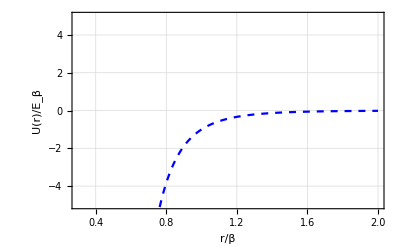

```mathematica
Show[uplots[[1]],PlotRange->{-5,5}]
```

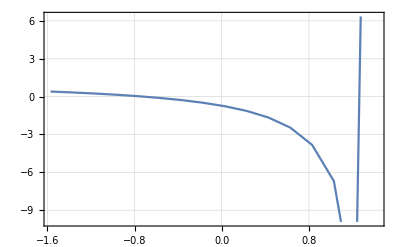

```mathematica
ListPlot[Table[{tf,QuantumDefectParameters[ArcTan[tf],ltest,3.0,0.0001][[3]]},{tf,-π/2,π/2,0.2}],Joined->True,GridLines->Automatic,Frame->True]
```

Okay, so now we can try to calculate the phase shifts and bound states.

```mathematica
Simplify[Normal[Series[√R BesselJ[-1/4(2L+1),x],{x,0,1}]]/.x->1/(2 R^2),R>0]
```

(2^(1/2+L) R^(1+L))/Gamma[3/4-L/2]

```mathematica
Simplify[Normal[Series[√R BesselJ[1/4(2L+1),x],{x,0,1}]]/.x->1/(2 R^2),R>0]
```

(2^(-1/2-L) R^-L)/Gamma[5/4+L/2]

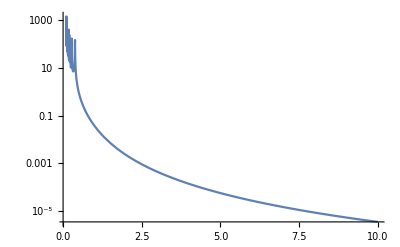

```mathematica
LogPlot[Abs[((2^(-1/2-L) R^-L)/Gamma[5/4+L/2]-χminus[L,R])/χminus[L,R]]/.L->1,{R,.1,10}]
```

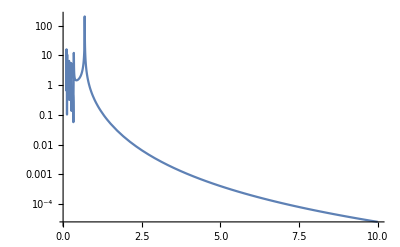

```mathematica
LogPlot[Abs[((2^(1/2+L) R^(1+L))/Gamma[3/4-L/2]-χplus[L,R])/χplus[L,R]]/.L->1,{R,.1,10}]
```

(2^(1/2+L)  √R)/Gamma[1+1/4 (-1-2 L)](R^2)^(+1/4+L/2)=2^(1/2+L)/Gamma[1+1/4 (-1-2 L)](R)^(+1+L)

### Energy dependence of the QDT parameter ϕ?

Is there a way to determine the energy dependence of the parameter ϕ near threshold?  Perhaps we can derive an equation obeyed by the energy derivative of the Milne solution?

Let’s start with the Schrodinger equation, considering ψ(E,r)

(∂^2/(∂r^2)+(2μ)/ℏ^2(E-V(r)-(ℏ^2 l(l+1))/(2μ r^2)))ψ(E,r)=0

∂/(∂E)(∂^2/(∂r^2)+(2μ)/ℏ^2(E-V(r)-(ℏ^2 l(l+1))/(2μ r^2)))ψ(E,r)=0

(∂^2/(∂r^2)(∂ψ(E,r))/(∂E)+(2μ)/ℏ^2(E (∂ψ(E,r))/(∂E)+ψ(E,r)-V(r)(∂ψ(E,r))/(∂E)-(ℏ^2 l(l+1))/(2μ r^2)(∂ψ(E,r))/(∂E)))=0

Which, at zero energy becomes:

(∂^2/(∂r^2)(∂ψ(E,r))/(∂E)+(2μ)/ℏ^2(ψ(E,r)-V(r)(∂ψ(E,r))/(∂E)-(ℏ^2 l(l+1))/(2μ r^2)(∂ψ(E,r))/(∂E)))=0

So it looks like we end up with a mixed equation that involves ψ(E,r).

(∂^2/(∂r^2)+k^2(r))ψ(r)=0

SInce we want V(r)→-C_6/r^6, we move to scaled units where the unit of length is β_6=(2μ C_6/ℏ^2)^(1/4) and energy is measured in units of ℏ^2/2μ β_6^2.

U(r)=V(r)+(ℏ^2 l(l+1))/(2μ r^2)→-1/r^6+(l(l+1))/r^2

So

k^2(r)=ϵ+1/r^6-(l(l+1))/r^2

Milne showed [W.E. Milne, Phys. Rev. 35, 863 (1930); Am. Math. Mon. 40, 322 (1933)] that the solution can be written

ψ(r)=a α(r) sin(∫_0^r α^-2(r')ⅆr'+b)

This result is valid provided that α(r) is any particular solution to Milne’s second-order, nonlinear differential equation:

(∂^2 α(r))/(∂r^2)+k^2(r)α(r)=1/(α^3(r))

```mathematica
((60^3 400)+60^2+(60 400)^2 3 8)/1024.^3
```

12.9551

```mathematica
12.955072894692421/64
```

0.202423

13./64

The number of half wavelengths inside a well of depth V_0 for a zero-energy solution is n:

n=√((V_0 2μ r_0^2)/(ℏ^2 π^2))

```mathematica
√((V0 r0^2)/π^2)/.{V0->10/r0^6}/.r0->0.2
```

25.1395